```mathematica
(* Quits the kernel incase other packages are installed that overlap with functions defined below*)
Quit[]
```

```mathematica
(* Parameterizations *)
LH[mh_]:=Log[mh/125.7];ΔH[mh_]:=mh/125.7-1;Δt[mt_]:=(mt/173.2)^2-1;
dH[mh_]:=Log[mh/100];
dh[mh_]:=(mh/100)^2;
dt[mt_]:=(mt/174.3)^2-1;

a1=-.1202;a2=-.06919;a3=.00383;
a4=.0597;a5=.8037;a6=-.015;
a7=-.0195;a8=.0032;
Γ[mh_,mt_]:=83.983+a1 LH[mh]+a2 LH[mh]^2+a3 LH[mh]^4+a4 ΔH[mh]+a5 Δt[mt]+a6 Δt[mt]^2+a7 Δt[mt]LH[mh]+a8 Δt[mt]LH[mh]^2

s0=2314.64;d1=4.616;d2=0.539;
d3=-.0737;d5=-25.71;d6=4.;
d7=.288;

sθ2[mh_,mt_]:=10^(-4)(s0+d1 LH[mh]+d2 LH[mh]^2+d3 LH[mh]^4+d5 Δt[mt]+d6 Δt[mt]^2+d7 Δt[mt]LH[mh])

mw0=80.3779;c1=.05427;c2=.008931;
c3=.0000883;c4=.000161;c6=.5237;
c7=.0679;c8=.00179;c9=.0000664;
mw[mh_,mt_]:=mw0-c1 dH[mh]-c2 dH[mh]^2+c3 dH[mh]^4+c4(dh[mh]-1)+c6 dt[mt]-c7 dt[mt]^2-c8 dH[mh]dt[mt]+c9 dh[mh]dt[mt];
```

```mathematica
(*Define chi2*)
χ2[mh_,mt_]:=((Γ[mh,mt]-83.92)/.12)^2+((sθ2[mh,mt]-.23153)/.00016)^2+((mw[mh,mt]-80.379)/.012)^2
```

{0.79885,{mh→268.105,mt→184.209}}

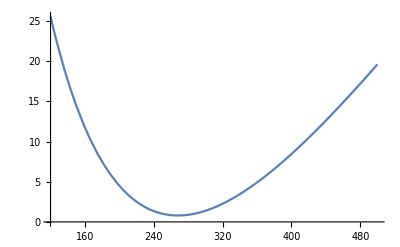

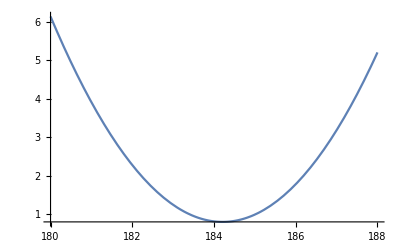

```mathematica
(*Minimize, and plot regions about best fit point for one mass set to best fit value*)
Minimize[{χ2[mh,mt],mh>0,mt>0},{mh,mt}]
Plot[χ2[mh,mt]/.mt->184.209,{mh,120,500}]
Plot[χ2[mh,mt]/.mh->268.105,{mt,180,188}]
```

```mathematica
(* Hold mh constant, solve for mt 1 sigma regions*)
NSolve[((χ2[mh,mt]/.mh->268.105)-0.79885)==1,mt,Reals]
186.02-184.209
184.209-182.392
```

{{mt→-186.02},{mt→-182.392},{mt→182.392},{mt→186.02}}

1.811

1.817

```mathematica
(* Hold mt constant, solve for 1 sigma regions*)
NSolve[((χ2[mh,mt]/.mt->184.209)-0.79885)==1,mh,Reals]
310.497-268.105
268.105-230.668
```

{{mh→230.668},{mh→310.497}}

42.392

37.437

{1.94951,{mh→98.764}}

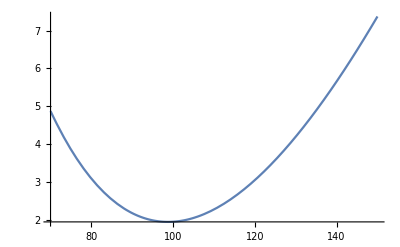

{{mh→81.1215},{mh→118.915}}

```mathematica
(* set mt to measured value, fit mh, plot regions*)
Minimize[{χ2[mh,173],mh>0},{mh}]
Plot[χ2[mh,173],{mh,70,150}]
NSolve[χ2[mh,173]-1.94951==1,mh,Reals]
```

```mathematica
118.915-98.764
98.764-81.1215
```

20.151

17.6425

```mathematica
(* Chi2[measured]-Chi2_min is an estimate of how many sigma the measured values are from SM predictions *)
χ2[125,173]-1.94951
```

1.63386